# Zero aliasing saturation

## Set Sample Rate

```mathematica
sampleRate = 48000;
```

## Sine sweep for testing

```mathematica
LogarithmicSineSweep[startFreq_,endFreq_,lengthSeconds_,sampleRate_]:=Module[{output,lengthSamples,i,phase=0,phaseIncrement,frequency},lengthSamples=N[lengthSeconds*sampleRate];
output=Table[0,{t,1,lengthSamples}];
For[i=1,i≤lengthSamples,i++,output[[i]]=Sin[N[phase]];
frequency=2^(Log2[startFreq]+Log2[endFreq/startFreq](i/lengthSamples));
phaseIncrement=2 π frequency/sampleRate;
phase+=phaseIncrement;
If[phase > 2π,phase -= 2π];
];
output]

(* six second sine sweep *)
sineSweep = LogarithmicSineSweep[20,sampleRate/2,6,sampleRate];
```

## Tones for testing

```mathematica
tone400Hz = Table[Sin[t 400 2 π / sampleRate],{t,1,2*sampleRate}];
tone20Hz = Table[Sin[t 20 2 π / sampleRate],{t,1,2*sampleRate}];
tone10000Hz = Table[Sin[t 10000 2 π / sampleRate],{t,1,2*sampleRate}];
```

## Quadratic Threshold functions

```mathematica
qLowerThreshold[x_,l_,w_]:=If[x<l-w,l,If[x>l+w,x,(-l x+(l+w+x)^2/4)/w]]
qUpperThreshold[x_,l_,w_]:=-If[w<-l+x,-l,If[-x>-l+w,-x,(l (-x)+1/4 (-l+w-x)^2)/w]]
```

## Antialiasing filters

```mathematica
ic11=0;
ic21=0;
a1s=0;
a2s=0;
a3s = 0;
SVFLowpass1[x_]:=Module[{v1,v2,v3},v3=x-ic21;
v1=a1s*ic11+a2s*v3;
v2=ic21+a2s*ic11+a3s*v3;
ic11=2*v1-ic11;
ic21=2*v2-ic21;
v2]
ic12=0;
ic22=0;
SVFLowpass2[x_]:=Module[{v1,v2,v3},v3=x-ic22;
v1=a1s*ic12+a2s*v3;
v2=ic22+a2s*ic12+a3s*v3;
ic12=2*v1-ic12;
ic22=2*v2-ic22;
v2]
ic13=0;
ic23=0;
SVFLowpass3[x_]:=Module[{v1,v2,v3},v3=x-ic23;
v1=a1s*ic13+a2s*v3;
v2=ic23+a2s*ic13+a3s*v3;
ic13=2*v1-ic13;
ic23=2*v2-ic23;
v2]
ic14=0;
ic24=0;
SVFLowpass4[x_]:=Module[{v1,v2,v3},v3=x-ic24;
v1=a1s*ic14+a2s*v3;
v2=ic24+a2s*ic14+a3s*v3;
ic14=2*v1-ic14;
ic24=2*v2-ic24;
v2]

ic15=0;
ic25=0;
SVFLowpass5[x_]:=Module[{v1,v2,v3},
v3=x-ic25;
v1=a1s*ic15+a2s*v3;
v2=ic25+a2s*ic15+a3s*v3;
ic15=2*v1-ic15;
ic25=2*v2-ic25;
v2]
ic16=0;
ic26=0;
SVFLowpass6[x_]:=Module[{v1,v2,v3},
v3=x-ic26;
v1=a1s*ic16+a2s*v3;
v2=ic26+a2s*ic16+a3s*v3;
ic16=2*v1-ic16;
ic26=2*v2-ic26;
v2]
ic17=0;
ic27=0;
SVFLowpass7[x_]:=Module[{v1,v2,v3},
v3=x-ic27;
v1=a1s*ic17+a2s*v3;
v2=ic27+a2s*ic17+a3s*v3;
ic17=2*v1-ic17;
ic27=2*v2-ic27;
v2]
ic18=0;
ic28=0;
SVFLowpass8[x_]:=Module[{v1,v2,v3},
v3=x-ic28;
v1=a1s*ic18+a2s*v3;
v2=ic28+a2s*ic18+a3s*v3;
ic18=2*v1-ic18;
ic28=2*v2-ic28;
v2]

setFcAndQAAFilters[fc_,Q_,sampleRate_]:=Module[{g=Tan[π fc/(sampleRate)],k=1/Q},
a1s=N[1/(1+g*(g+k))];
a2s=N[g*a1s];
a3s=N[g*a2s];
]
```

## Rectifier using quadratic threshold

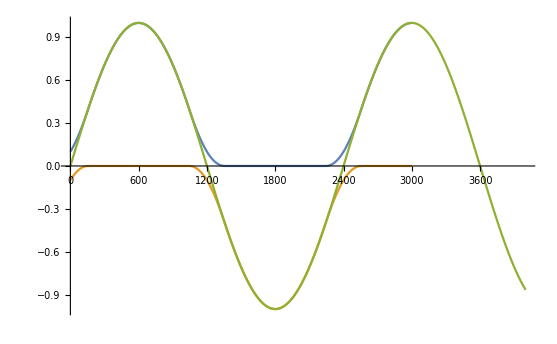

```mathematica
posRect =qLowerThreshold[#,0,0.4]&/@tone20Hz;
negRect =qUpperThreshold[#,0,0.4]&/@tone20Hz;
ListLinePlot[{posRect[[1;;3000]],negRect[[1;;3000]],posRect[[1;;4000]]+negRect[[1;;4000]]}]
```

## Waveshaping function on [-1,1] with continuous derivatives at the boundaries

```mathematica
f1[x_,a_,b_,c_,d_]:=a x^3 + b x^2 + c x + d 
f1p[x_,a_,b_,c_]:=3 a x^2 + 2 b x + c
Solve[f1[-1,a,b,c,d]==-1 &&f1p[-1,a,b,c]==0 &&f1[1,a,b,c,d]==1 &&f1p[1,a,b,c]==0,{a,b,c,d}]
```

{{a→-1/2,b→0,c→3/2,d→0}}

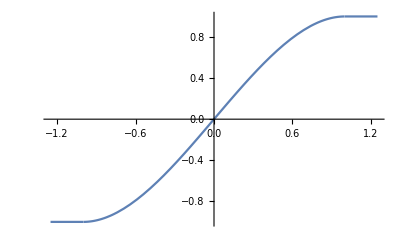

```mathematica
waveshaping[x_]:=-(1/2)Clip[x]^3 + (3/2)Clip[x]
Plot[waveshaping[x],{x,-1.25,1.25}]
```

## Waveshaping function on [0,1] with continuous derivative at 1 *This looks better than the cubic one on [-1,1]*

```mathematica
f1[x_,a_,b_,c_]:=a x^2 + b x + c 
f1p[x_,a_,b_]:=2a x + b
Solve[f1[0,a,b,c]==0 &&f1[1,a,b,c]==1 &&f1p[1,a,b]==0,{a,b,c}]
```

{{a→-1,b→2,c→0}}

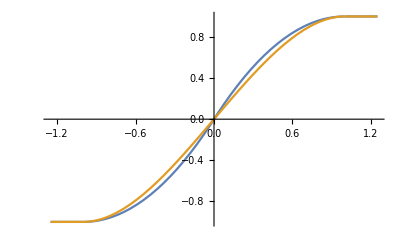

```mathematica
waveshapingPos[x_]:=2 Clip[x]-Clip[x]^2
waveshapingNeg[x_]:=2 Clip[x]+Clip[x]^2
signedMin[x_,y_]:=If[Abs[x]<Abs[y],x,y]
Plot[{signedMin[waveshapingPos[x],waveshapingNeg[x]],waveshaping[x]},{x,-1.25,1.25}]
```

## Waveshaping rectified signal

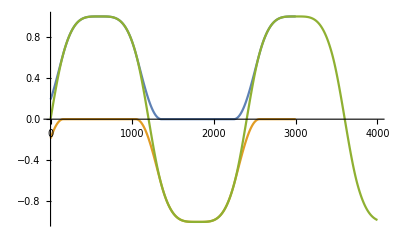

```mathematica
posRect =qLowerThreshold[#,0,0.4]&/@tone20Hz;
negRect =qUpperThreshold[#,0,0.4]&/@tone20Hz;
posRectShaped =waveshapingPos[posRect];
negRectShaped = waveshapingNeg[negRect];
ListLinePlot[{posRectShaped[[1;;3000]],negRectShaped[[1;;3000]],posRectShaped[[1;;4000]]+negRectShaped[[1;;4000]]}]
```

## Convert the waveshaping to a control signal

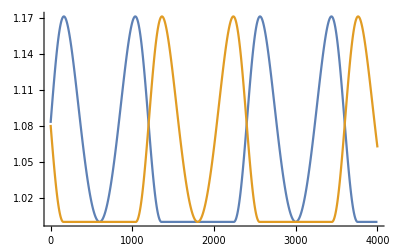

```mathematica
posRect =qLowerThreshold[#,0,0.4]&/@tone20Hz;
negRect =qUpperThreshold[#,0,0.4]&/@tone20Hz;
posRectShaped =waveshapingPos[posRect];
negRectShaped = waveshapingNeg[negRect];

posRectBiased = posRect + 1;
negRectBiased = negRect -1;
posRectShapedBiased = posRectShaped + 1;
negRectShapedBiased = negRectShaped -1;

posControlSignal = posRectShapedBiased / posRectBiased;
negControlSignal = negRectShapedBiased / negRectBiased;

ListLinePlot[{posControlSignal[[1;;4000]],negControlSignal[[1;;4000]]}]
```

## Apply anti-aliasing filters to the control signals

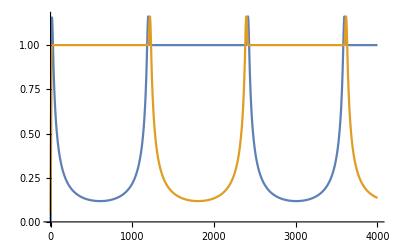

```mathematica
posRect =qLowerThreshold[#,0,0.4]&/@(16tone20Hz);
negRect =qUpperThreshold[#,0,0.4]&/@(16tone20Hz);
posRectShaped =waveshapingPos[posRect];
negRectShaped = waveshapingNeg[negRect];

posRectBiased = posRect + 1;
negRectBiased = negRect -1;
posRectShapedBiased = posRectShaped + 1;
negRectShapedBiased = negRectShaped -1;

posControlSignal = posRectShapedBiased / posRectBiased;
negControlSignal = negRectShapedBiased / negRectBiased;

(* set filter Q and cutoff frequency *)
criticallyDampedQ = 1/2;
setFcAndQAAFilters[5000,criticallyDampedQ,sampleRate];

(* apply the filters *)
posControlAA = SVFLowpass2/@(SVFLowpass1 /@ posControlSignal);
negControlAA = SVFLowpass4/@(SVFLowpass3 /@ negControlSignal);

ListLinePlot[{posControlAA[[1;;4000]],negControlAA[[1;;4000]]}]
```

## Use the anti-aliased control signals to do the waveshaping

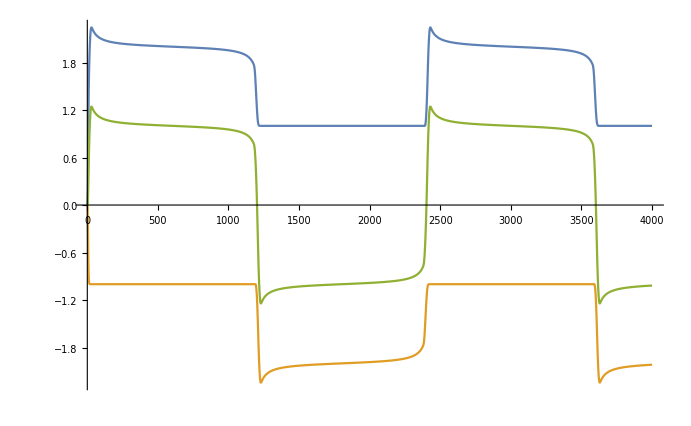

```mathematica
posRectBiasedShapedAA = posRectBiased * posControlAA;
negRectBiasedShapedAA = negRectBiased * negControlAA;

ListLinePlot[{posRectBiasedShapedAA[[1;;4000]],negRectBiasedShapedAA[[1;;4000]],posRectBiasedShapedAA[[1;;4000]]+negRectBiasedShapedAA[[1;;4000]]}]
```

## Test on a sine sweep

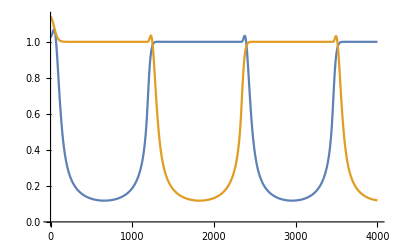

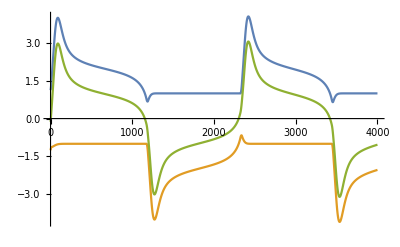

```mathematica
posRect =qLowerThreshold[#,0,0.4]&/@(16sineSweep);
negRect =qUpperThreshold[#,0,0.4]&/@(16sineSweep);
posRectShaped =waveshapingPos[posRect];
negRectShaped = waveshapingNeg[negRect];

posRectBiased = posRect + 1;
negRectBiased = negRect -1;
posRectShapedBiased = posRectShaped + 1;
negRectShapedBiased = negRectShaped -1;

posControlSignal = posRectShapedBiased / posRectBiased;
negControlSignal = negRectShapedBiased / negRectBiased;

(* set filter Q and cutoff frequency *)
criticallyDampedQ = 1/2;
setFcAndQAAFilters[500,criticallyDampedQ,sampleRate];

(* apply the filters *)
posControlAA = SVFLowpass2/@(SVFLowpass1 /@ posControlSignal);
negControlAA = SVFLowpass4/@(SVFLowpass3 /@ negControlSignal);

ListLinePlot[{posControlAA[[1;;4000]],negControlAA[[1;;4000]]}]

posRectBiasedShapedAA = posRectBiased * posControlAA;
negRectBiasedShapedAA = negRectBiased * negControlAA;

output = posRectBiasedShapedAA+negRectBiasedShapedAA;

ListLinePlot[{posRectBiasedShapedAA[[1;;4000]],negRectBiasedShapedAA[[1;;4000]],output[[1;;4000]]}]

Export["/Users/hansanderson/Desktop/saturatorTest.wav",ListPlay[output,SampleRate->48000,PlayRange->All]];
```

## Combine both control signals into one

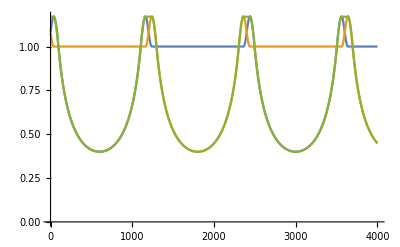

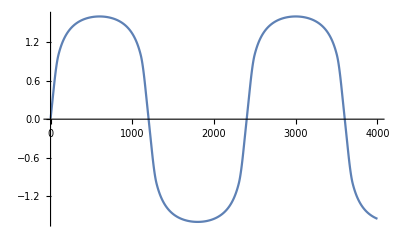

```mathematica
posRect =qLowerThreshold[4#,0,0.4]&/@tone20Hz[[1;;4000]];
negRect =qUpperThreshold[4#,0,0.4]&/@tone20Hz[[1;;4000]];
posRectShaped =waveshapingPos[posRect];
negRectShaped = waveshapingNeg[negRect];

posRectBiased = posRect + 1;
negRectBiased = negRect -1;
posRectShapedBiased = posRectShaped + 1;
negRectShapedBiased = negRectShaped -1;

posControlSignal = posRectShapedBiased / posRectBiased;
negControlSignal = negRectShapedBiased / negRectBiased;
(* combinedControlSignal = (posControlSignal^2 + negControlSignal^2)/2; *)
(* combinedControlSignal = 2^(Log2[posControlSignal] + Log2[negControlSignal]); *)
combinedControlSignal = posControlSignal *negControlSignal;

ListLinePlot[{posControlSignal,negControlSignal,combinedControlSignal}]
ListLinePlot[combinedControlSignal*(posRect+negRect)]
```

## Anti-alias the combined control signal

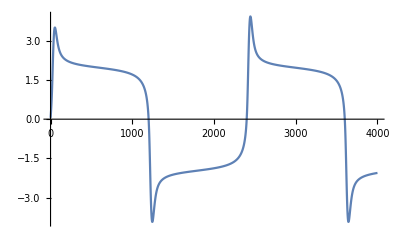

```mathematica
signal = 48tone20Hz[[1;;4000]];
posRect =qLowerThreshold[#,0,0.4]&/@signal;
negRect =qUpperThreshold[#,0,0.4]&/@signal;
posRectShaped =waveshapingPos[posRect];
negRectShaped = waveshapingNeg[negRect];

posRectBiased = posRect + 1;
negRectBiased = negRect -1;
posRectShapedBiased = posRectShaped + 1;
negRectShapedBiased = negRectShaped -1;

posControlSignal = posRectShapedBiased / posRectBiased;
negControlSignal = negRectShapedBiased / negRectBiased;

(* set filter Q and cutoff frequency *)
criticallyDampedQ = 1/2;
setFcAndQAAFilters[1000,criticallyDampedQ,sampleRate];

(* apply the filters *)
posControlAA = SVFLowpass2/@(SVFLowpass1 /@ posControlSignal);
negControlAA = SVFLowpass4/@(SVFLowpass3 /@ negControlSignal);

combinedControlAA = 2^(Log2[posControlAA] + Log2[negControlAA]);

ListLinePlot[{combinedControlAA*signal}]
```

## Soft clip with linear gain below threshold

```mathematica
softClipWLinear[x_,threshold_,limit_]:=qLowerThreshold[qUpperThreshold[x,limit,limit-threshold],-limit,limit-threshold]
```

## Funky Clipping that dips down for high values

```mathematica
f2[x_,a_,b_,c_,d_]:=a x^3 + b x^2 + c x + d
f2p[x_,a_,b_,c_]:=3 a x^2 + 2 b x + c
Solve[f2[0,a,b,c,d]==0&&f2p[1,a,b,c]==0&&f2[1,a,b,c,d]==endY&&f2p[peakX,a,b,c]==0,{a,b,c,d}]//FullSimplify
groovyClipPos[x_,endY_,peakX_]:= (2 endY)/(-1+3 peakX)Clip[x]^3-(3 endY (1+peakX))/(-1+3 peakX)Clip[x]^2 + (6 endY peakX)/(-1+3 peakX)Clip[x]
groovyClipNeg[x_,endY_,peakX_] := -groovyClipPos[-x,-endY,peakX]
groovyClipBothSides[x_,endY_,peakX_]:=If[x>0,groovyClipPos[x,endY,peakX],groovyClipNeg[x,-endY,peakX]]
```

{{a→(2 endY)/(-1+3 peakX),b→-(3 endY (1+peakX))/(-1+3 peakX),c→(6 endY peakX)/(-1+3 peakX),d→0}}

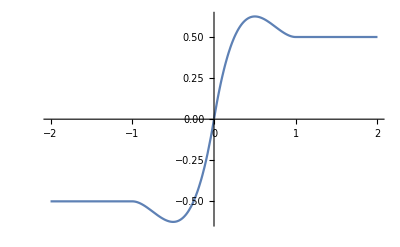

```mathematica
Plot[groovyClipBothSides[x,0.5,0.5],{x,-2,2}]
```

## Zavalishin LPF

```mathematica
(* LPF from 3.18 of The Art of Virtual Analog Filter Design by V. Zavalishin *)
lpfZ1State1=0;
lpfZ1State2=0;
lpfZ1State3=0;
lpfZ1State4=0;
lpfZ1State5=0;
lpfZ1State6=0;
lpfZ1State7=0;
lpfZ1State8=0;
lpfGOdd = 0; (* G = g/(1+g) *)
lpfGEven = 0;
prevOut = 0;

zavalishinLPF1[x_]:=Module[{v,y},
v = (x - lpfZ1State1)*lpfGOdd;
y = v+ lpfZ1State1;
lpfZ1State1 = y + v;
y
]
zavalishinLPF2[x_]:=Module[{v,y},
v = (x - lpfZ1State2)*lpfGEven;
y = v+ lpfZ1State2;
lpfZ1State2 = y + v;
y
]
zavalishinLPF3[x_]:=Module[{v,y},
v = (x - lpfZ1State3)*lpfGOdd;
y = v+ lpfZ1State3;
lpfZ1State3 = y + v;
y
]
zavalishinLPF4[x_]:=Module[{v,y},
v = (x - lpfZ1State4)*lpfGEven;
y = v+ lpfZ1State4;
lpfZ1State4 = y + v;
y
]
zavalishinLPF5[x_]:=Module[{v,y},
v = (x - lpfZ1State5)*lpfGOdd;
y = v+ lpfZ1State5;
lpfZ1State5 = y + v;
y
]
zavalishinLPF6[x_]:=Module[{v,y},
v = (x - lpfZ1State6)*lpfGEven;
y = v+ lpfZ1State6;
lpfZ1State6 = y + v;
y
]
zavalishinLPF7[x_]:=Module[{v,y},
v = (x - lpfZ1State7)*lpfGOdd;
y = v+ lpfZ1State7;
lpfZ1State7 = y + v;
y
]
zavalishinLPF8[x_]:=Module[{v,y},
v = (x - lpfZ1State8)*lpfGEven;
y = v+ lpfZ1State8;
lpfZ1State8 = y + v;
y
]

zLPFSetFcOdd[fc_,sampleRate_]:=Module[{g},
g =fc / (2 sampleRate); (*zavalishin 3.11 *)
lpfGOdd = g/(1+g);
]
zLPFSetFcEven[fc_,sampleRate_]:=Module[{g},
g =fc / (2 sampleRate); (*zavalishin 3.11 *)
lpfGEven= g/(1+g);
]
```

## Test the single control signal on a sine sweep

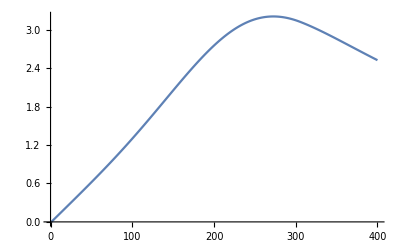

```mathematica
dBToGain[dB_]:=10^(dB/20)
criticallyDampedQ = 1/2;
signal = dBToGain[20](sineSweep); 
(* signal = dBToGain[20]Table[Sin[2000 2 π t],{t,0,1,1/sampleRate}]; *)
posRect =qLowerThreshold[#,0,1]&/@signal;
negRect =qUpperThreshold[#,0,1]&/@signal;

posRectLP = posRect;
negRectLP = negRect;

(* apply AA filters here, before waveshaping, so that aliasing will not occur *)
(*
setFcAndQAAFilters[45,criticallyDampedQ,sampleRate];
posRectLP = SVFLowpass1 /@ posRect;
negRectLP = SVFLowpass5 /@ negRect;
*)
(*
zLPFSetFcOdd[500,sampleRate];
zLPFSetFcEven[1000,sampleRate];
posRectLP = zavalishinLPF1 /@zavalishinLPF2 /@zavalishinLPF4 /@ posRect;
negRectLP = zavalishinLPF5 /@zavalishinLPF6 /@zavalishinLPF8 /@negRect;
*)

(*
zLPFSetFcOdd[600,sampleRate];
zLPFSetFcEven[600,sampleRate];
posRectLP = zavalishinLPF1 /@zavalishinLPF2/@ posRect;
negRectLP = zavalishinLPF5 /@zavalishinLPF6/@ negRect;
*)

fcAll=750;
zLPFSetFcOdd[fcAll,sampleRate];
posRectLP = zavalishinLPF1 /@posRectLP;
negRectLP = zavalishinLPF5 /@negRectLP;
zLPFSetFcEven[fcAll,sampleRate];
posRectLP = zavalishinLPF2 /@posRectLP;
negRectLP = zavalishinLPF6 /@negRectLP;
zLPFSetFcOdd[fcAll,sampleRate];
posRectLP = zavalishinLPF3 /@posRectLP;
negRectLP = zavalishinLPF7 /@negRectLP;
zLPFSetFcEven[fcAll,sampleRate];
posRectLP = zavalishinLPF4 /@posRectLP;
negRectLP = zavalishinLPF8 /@negRectLP;



(*
setFcAndQAAFilters[100,(1/2),sampleRate];
posRectLP = SVFLowpass1/@posRectLP;
negRectLP = SVFLowpass2 /@ negRectLP;
*)

(* apply a second stage of AA filters at a higher cutoff frequency *)
(*setFcAndQAAFilters[1000,criticallyDampedQ,sampleRate];
posRectLP = SVFLowpass1 /@SVFLowpass2/@ SVFLowpass3/@posRectLP;
negRectLP = SVFLowpass5 /@SVFLowpass6 /@SVFLowpass7/@ negRectLP; *)

(*zLPFSetFcOdd[1000,sampleRate];
zLPFSetFcEven[2000,sampleRate];
posRectLP = zavalishinLPF2/@zavalishinLPF3/@ posRectLP;
negRectLP = zavalishinLPF6/@zavalishinLPF7/@ negRectLP;
zLPFSetFcEven[4000,sampleRate];
posRectLP = zavalishinLPF4 /@posRectLP;
negRectLP = zavalishinLPF8 /@negRectLP;*)


(* ordinary soft clipping function *)
posRectShaped =waveshapingPos[posRectLP];
negRectShaped = waveshapingNeg[negRectLP];

posRectBiased = posRectLP + 1;
negRectBiased = negRectLP -1;
posRectShapedBiased = posRectShaped + 1;
negRectShapedBiased = negRectShaped -1;

posControlSignal = posRectShapedBiased / posRectBiased;
negControlSignal = negRectShapedBiased / negRectBiased;

output = posControlSignal*(posRect +1) + negControlSignal * (negRect -1);

(* output = combinedControlAA*signal; *)

(* soft clip the output to prevent it from peaking too high *)
(*output = softClipWLinear[#,3.25,2.4]&/@output; *)
ListLinePlot[{output[[1;;400]]},PlotRange->All]

Export["/Users/hansanderson/Desktop/saturatorTest.wav",ListPlay[output,SampleRate->48000,PlayRange->All]];
```

## Correction Filters? The method above gives a boost at 80HZ (with 4 first order AA filters at 760 Hz) Should we filter it back down?

## Can we find second order critically damped filters that match the frequency response of the first order filter cascade (in order to use vDSP optimized biquad filters)? Answer: Yes. Use two critically damped lowpass filters to replace the four first order lowpass filters. Set the cutoff to about 1/6 of what you set for the first order filters because the cutoff seems to be wrong in the first order formula.

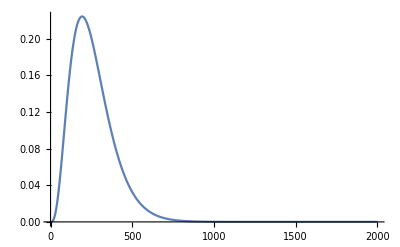

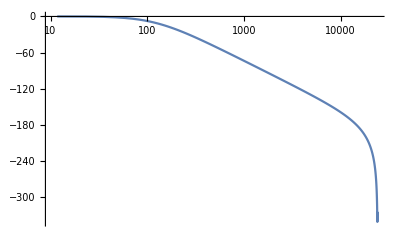

```mathematica
testLength = 2^12;
zeros = Table[0,{x,0,testLength}];
impulse = zeros;
impulse[[1]] =testLength^(1/2);
sampleRate=48000;
fcAll = 750;
zLPFSetFcOdd[fcAll,sampleRate];
zLPFSetFcEven[fcAll,sampleRate];
zavalishinLPF1 /@ zeros;
zavalishinLPF2 /@ zeros;
zavalishinLPF3 /@ zeros;
zavalishinLPF4 /@ zeros;
IR =  zavalishinLPF4/@(zavalishinLPF3/@(zavalishinLPF2 /@(zavalishinLPF1 /@ impulse)));
ListLinePlot[IR[[1;;2000]],PlotRange->All]
fourierIR = Abs[Fourier[IR][[1;;testLength/2]]];
gainToDB[g_]:=20Log10[g]
ListLogLinearPlot[gainToDB/@fourierIR,PlotRange->All,DataRange->{(sampleRate/2)/(testLength/2),sampleRate/2},Joined->True]
```

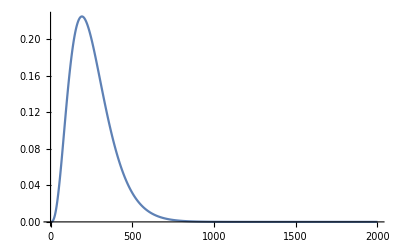

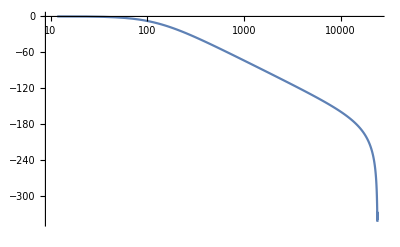

```mathematica
testLength = 2^12;
zeros = Table[0,{x,0,testLength}];
impulse = zeros;
impulse[[1]] = testLength^(1/2);
sampleRate=48000;
fcSVF = 120;
QSVF = 0.5; 
ic11=0;
ic21=0;
ic12=0;
ic22=0;
setFcAndQAAFilters[fcSVF,QSVF,48000];
IR =  SVFLowpass2/@(SVFLowpass1 /@ impulse);
ListLinePlot[IR[[1;;2000]],PlotRange->All]
fourierIR = Abs[Fourier[IR][[1;;testLength/2]]];
gainToDB[g_]:=20Log10[g]
ListLogLinearPlot[gainToDB/@fourierIR,PlotRange->All,DataRange->{(sampleRate/2)/(testLength/2),sampleRate/2},Joined->True]
```

## Does the SVF filter give the same or similar output to the Biquad filters in the app? Answer: No. Not even close. The SVF looks nice but the biquad looks terrible.

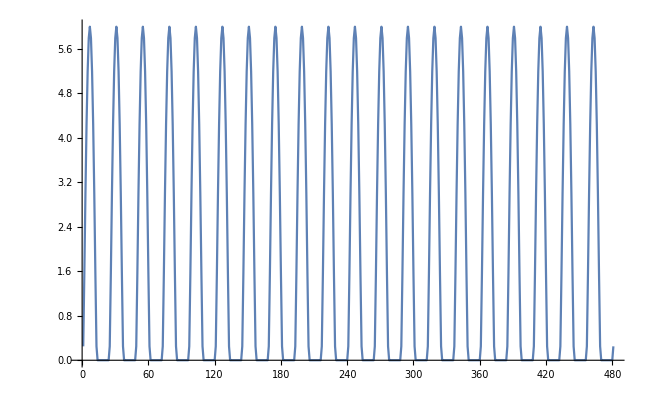

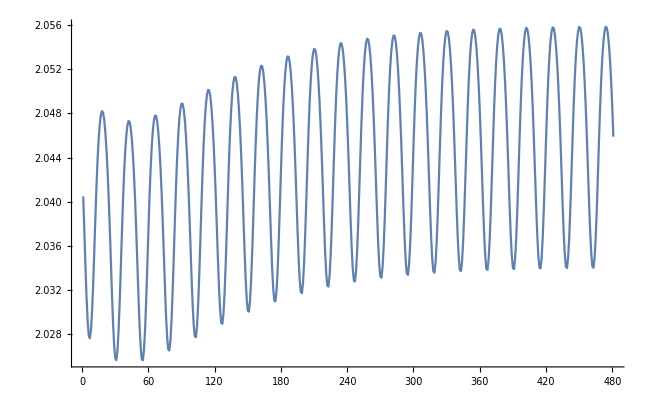

```mathematica
signal = 6Table[Sin[2000 2 π t],{t,0,0.01,1/sampleRate}];
signal =(qLowerThreshold[#,0,1]&/@signal);
ListLinePlot[signal,PlotRange->All]
setFcAndQAAFilters[125.0,0.5,48000];
signal = SVFLowpass1/@(qLowerThreshold[#,0,1]&/@signal);
ListLinePlot[signal,PlotRange->All]
```

(0.0000658536+0.000131707 z+0.0000658536 z^2)/(-0.967803+1.96754 z-z^2)

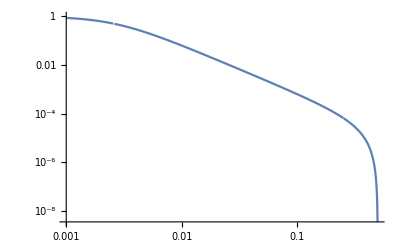

```mathematica
h[z_]=(0.000065853566831957153 z^2 + 0.00013170713366391431 z + 0.000065853566831957153)/(-1 z^2 +1.9675399157531697 z - 0.96780333002049756 )
LogLogPlot[Abs[h[ⅇ^(ω ⅈ 2 π)]],{ω,0.001,1/2}]
```